## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = False;

rxnName="FBA2";
fitLabel="all_fixed";
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Desktop/MASSef/";
kineticDataFileName =  "kinetic_data_MASSef.csv";

mainFolder = "fit_FBA2";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/MASSef/examples/FBA2/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{fdp,Null,Keq substrate}

{0.00016,Keq value}

{fdp,Km or S05 substrate}

{0.00017,Km or S05 value}

{{{fdp,Null}},kcat substrates}

{10.5,kcat value}

{dhap,Inhibition or activation constant substrate}

{0.00013,Inhibition or activation constant value}

{g3p,Inhibition or activation constant substrate}

{0.00003,Inhibition or activation constant value}

{g3p,Inhibition or activation constant substrate}

{0.00023,Inhibition or activation constant value}

{{{fdp,Null}},kcat substrates}

{8.17,kcat value}

{fdp,Km or S05 substrate}

{0.00019,Km or S05 value}

{dhap,Inhibition or activation constant substrate}

{9.×10^-6,Inhibition or activation constant value}

{g3p,Inhibition or activation constant substrate}

{0.000118,Inhibition or activation constant value}

{g3p,Inhibition or activation constant substrate}

{0.000221,Inhibition or activation constant value}

{{{fdp,Null}},kcat substrates}

{10.33,kcat value}

{fdp,Km or S05 substrate}

{0.00024,Km or S05 value}

{fdp,Km or S05 substrate}

{0.00085,Km or S05 value}

(fdp^c⇌dhap^c+g3p^c)^FBA2

Ordered Sequential Uni Bi; [fdp,g3p,dhap]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp,Null | 0.00016 | 0.000152
0.000168 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00017 | 0.000167
0.000173 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00019 | 0.00016
0.00022 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00024 | 0.00021
0.00027 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00085 | 0.0008075
0.0008925 |  | M | 7.5 | 30 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 10.5 | 9.83
11.2 | 1/s | 8 | 30 | trishcl | 0.05 | 
1 | fdp | Null | 8.17 | 7.73
8.6 | 1/s | 8 | 30 | trishcl | 0.05 | 
1 | fdp | Null | 10.33 | 10.03
10.63 | 1/s | 8 | 30 | trishcl | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | dhap | 0.00013 | 0.000119
0.000141 |  | Competitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincc | g3p | 0.00003 | 0.000025
0.000035 |  | NonCompetitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincu | g3p | 0.00023 | 0.000188
0.000272 |  | NonCompetitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kic | dhap | 9.×10^-6 | 7.8×10^-6
0.0000102 |  | Competitive | fdp | 0.00019 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincc | g3p | 0.000118 | 0.000095
0.000141 |  | NonCompetitive | fdp | 0.00019 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincu | g3p | 0.000221 | 0.000194
0.000248 |  | NonCompetitive | fdp | 0.00019 | M | 8 | 30 | trishcl | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,0,0,0};
s05Priorities = Null;
kcatPriorities = {1,0,0};
inhibitionPriorities={1,1,1,0,0,0};
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(fdp^c⇌dhap^c+g3p^c)^FBA2

Ordered Sequential Uni Bi; [fdp,g3p,dhap]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp,Null | 0.00016 | 0.000152
0.000168 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00017 | 0.000167
0.000173 |  | M | 8 | 30 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 10.5 | 9.83
11.2 | 1/s | 8 | 30 | trishcl | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | dhap | 0.00013 | 0.000119
0.000141 |  | Competitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincc | g3p | 0.00003 | 0.000025
0.000035 |  | NonCompetitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincu | g3p | 0.00023 | 0.000188
0.000272 |  | NonCompetitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
rxn
```

(fdp^c⇌dhap^c+g3p^c)^FBA2

```mathematica
catalyticBranch={"E_FBA2[c] + fdp[c] <=> E_FBA2[c]&fdp",
				"E_FBA2[c]&fdp <=> E_FBA2[c]&dhap&g3p",
				"E_FBA2[c]&dhap&g3p <=> E_FBA2[c]&dhap + g3p[c]",
				"E_FBA2[c]&dhap <=> E_FBA2[c] + dhap[c]"};

enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModelOrig["Reactions"]
```

{((FBA2^c)_^+fdp^c⇌(FBA2^c&fdp^c)_^)^FBA21,((FBA2^c&dhap^c)_^⇌(FBA2^c)_^+dhap^c)^FBA22,((FBA2^c&fdp^c)_^⇌(FBA2^c&dhap^c&g3p^c)_^)^FBA23,((FBA2^c&dhap^c&g3p^c)_^⇌(FBA2^c&dhap^c)_^+g3p^c)^FBA24}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1=enzymeModelOrig["Reactions"];
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
deleteDirectoryContents[inputPath]
Get["MASSef`"]
```

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc=1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={{"prod_inhib_dhap",m["g3p","c"]->0},{"prod_inhib_g3p",m["dhap","c"]->0}};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

{fdp^c→0}

{dhap^c→0,g3p^c→0}

{fdp^c→1}

{dhap^c→1,g3p^c→1}

prod inhib

Loading flux equation...

Added inhibition reactions:

{((FBA2^c)_^+dhap^c⇌(FBA2^c&dhap^c)_^)^FBA2_Kic_dhap_1_fdp,((FBA2^c)_^+g3p^c⇌(FBA2^c&g3p^c)_^)^FBA2_Kincc_g3p_1_fdp,((FBA2^c&g3p^c)_^+fdp^c⇌(FBA2^c&fdp^c&g3p^c)_^)^FBA2_NC_g3p,((FBA2^c&fdp^c)_^+g3p^c⇌(FBA2^c&fdp^c&g3p^c)_^)^FBA2_Kincu_g3p_1_fdp}

Loading flux equation...

Loading absolute rate forward equation...

Loading absolute rate reverse equation...

Loading relative rate forward equation...

Loading relative rate reverse equation...

Loading relative rate reverse equation...

Generating other relative rate forward equation...

Simplifying...

{prod_inhib_dhap,g3p^c→0}

{fdp^c→1}

{prod_inhib_g3p,dhap^c→0}

{fdp^c→1}

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
enzymeModel["Reactions"]
```

{((FBA2^c)_^+fdp^c⇌(FBA2^c&fdp^c)_^)^FBA21,((FBA2^c&dhap^c)_^⇌(FBA2^c)_^+dhap^c)^FBA22,((FBA2^c&fdp^c)_^⇌(FBA2^c&dhap^c&g3p^c)_^)^FBA23,((FBA2^c&dhap^c&g3p^c)_^⇌(FBA2^c&dhap^c)_^+g3p^c)^FBA24,((FBA2^c)_^+dhap^c⇌(FBA2^c&dhap^c)_^)^FBA2_Kic_dhap_1_fdp,((FBA2^c)_^+g3p^c⇌(FBA2^c&g3p^c)_^)^FBA2_Kincc_g3p_1_fdp,((FBA2^c&g3p^c)_^+fdp^c⇌(FBA2^c&fdp^c&g3p^c)_^)^FBA2_NC_g3p,((FBA2^c&fdp^c)_^+g3p^c⇌(FBA2^c&fdp^c&g3p^c)_^)^FBA2_Kincu_g3p_1_fdp}

```mathematica
absoluteRateForward
```

(fdp^c FBA2_total_Global k_FBA21^⟶ k_FBA23^⟶ k_FBA24^⟶ (k_FBA22^⟶+k_FBA2_Kic_dhap_1_fdp^⟵))/(fdp^c k_FBA21^⟶ k_FBA23^⟶ k_FBA24^⟶+k_FBA22^⟶ (k_FBA23^⟶ (fdp^c k_FBA21^⟶+k_FBA24^⟶)+fdp^c k_FBA21^⟶ (k_FBA23^⟵+k_FBA24^⟶))+fdp^c k_FBA21^⟶ k_FBA23^⟵ k_FBA2_Kic_dhap_1_fdp^⟵+fdp^c k_FBA21^⟶ k_FBA23^⟶ k_FBA2_Kic_dhap_1_fdp^⟵+fdp^c k_FBA21^⟶ k_FBA24^⟶ k_FBA2_Kic_dhap_1_fdp^⟵+k_FBA23^⟶ k_FBA24^⟶ k_FBA2_Kic_dhap_1_fdp^⟵+k_FBA21^⟵ (k_FBA23^⟵+k_FBA24^⟶) (k_FBA22^⟶+k_FBA2_Kic_dhap_1_fdp^⟵))

```mathematica
relativeRateForward
```

{(fdp^c (k_FBA23^⟶ k_FBA24^⟶ (k_FBA22^⟶+k_FBA2_Kic_dhap_1_fdp^⟵)+k_FBA21^⟵ (k_FBA23^⟵+k_FBA24^⟶) (k_FBA22^⟶+k_FBA2_Kic_dhap_1_fdp^⟵)+k_FBA21^⟶ (k_FBA22^⟶ (k_FBA23^⟵+k_FBA23^⟶+k_FBA24^⟶)+(k_FBA23^⟵+k_FBA24^⟶) k_FBA2_Kic_dhap_1_fdp^⟵+k_FBA23^⟶ (k_FBA24^⟶+k_FBA2_Kic_dhap_1_fdp^⟵))))/(k_FBA23^⟶ k_FBA24^⟶ (k_FBA22^⟶+k_FBA2_Kic_dhap_1_fdp^⟵)+k_FBA21^⟵ (k_FBA23^⟵+k_FBA24^⟶) (k_FBA22^⟶+k_FBA2_Kic_dhap_1_fdp^⟵)+fdp^c k_FBA21^⟶ (k_FBA22^⟶ (k_FBA23^⟵+k_FBA23^⟶+k_FBA24^⟶)+(k_FBA23^⟵+k_FBA24^⟶) k_FBA2_Kic_dhap_1_fdp^⟵+k_FBA23^⟶ (k_FBA24^⟶+k_FBA2_Kic_dhap_1_fdp^⟵)))}

```mathematica
otherAbsoluteRatesForward
```

{{otherRateRelFor_fdp_prod_inhib_dhap,(fdp^c (k_FBA23^⟶ k_FBA24^⟶ (k_FBA22^⟶+k_FBA2_Kic_dhap_1_fdp^⟵)+k_FBA21^⟵ (k_FBA23^⟵+k_FBA24^⟶) (k_FBA22^⟶+k_FBA2_Kic_dhap_1_fdp^⟵)+k_FBA21^⟶ (k_FBA22^⟶ (k_FBA23^⟵+k_FBA23^⟶+k_FBA24^⟶)+(k_FBA23^⟵+k_FBA24^⟶) k_FBA2_Kic_dhap_1_fdp^⟵+k_FBA23^⟶ (k_FBA24^⟶+k_FBA2_Kic_dhap_1_fdp^⟵))))/(fdp^c k_FBA21^⟶ k_FBA22^⟶ k_FBA23^⟵+fdp^c k_FBA21^⟶ k_FBA22^⟶ k_FBA23^⟶+fdp^c k_FBA21^⟶ k_FBA22^⟶ k_FBA24^⟶+fdp^c k_FBA21^⟶ k_FBA23^⟶ k_FBA24^⟶+k_FBA22^⟶ k_FBA23^⟶ k_FBA24^⟶+fdp^c k_FBA21^⟶ k_FBA23^⟵ k_FBA2_Kic_dhap_1_fdp^⟵+fdp^c k_FBA21^⟶ k_FBA23^⟶ k_FBA2_Kic_dhap_1_fdp^⟵+fdp^c k_FBA21^⟶ k_FBA24^⟶ k_FBA2_Kic_dhap_1_fdp^⟵+k_FBA23^⟶ k_FBA24^⟶ k_FBA2_Kic_dhap_1_fdp^⟵+k_FBA21^⟵ (k_FBA23^⟵+k_FBA24^⟶) (k_FBA22^⟶+k_FBA2_Kic_dhap_1_fdp^⟵)+dhap^c (k_FBA23^⟶ k_FBA24^⟶+k_FBA21^⟵ (k_FBA23^⟵+k_FBA24^⟶)) (k_FBA22^⟵+k_FBA2_Kic_dhap_1_fdp^⟶))},{otherRateRelFor_fdp_prod_inhib_g3p,(fdp^c (k_FBA23^⟶ k_FBA24^⟶ (k_FBA22^⟶+k_FBA2_Kic_dhap_1_fdp^⟵)+k_FBA21^⟵ (k_FBA23^⟵+k_FBA24^⟶) (k_FBA22^⟶+k_FBA2_Kic_dhap_1_fdp^⟵)+k_FBA21^⟶ (k_FBA22^⟶ (k_FBA23^⟵+k_FBA23^⟶+k_FBA24^⟶)+(k_FBA23^⟵+k_FBA24^⟶) k_FBA2_Kic_dhap_1_fdp^⟵+k_FBA23^⟶ (k_FBA24^⟶+k_FBA2_Kic_dhap_1_fdp^⟵))) (g3p^c k_FBA2_Kincc_g3p_1_fdp^⟶ k_FBA2_Kincu_g3p_1_fdp^⟵ k_FBA2_NC_g3p^⟶+k_FBA21^⟶ (k_FBA2_Kincc_g3p_1_fdp^⟵ (k_FBA2_Kincu_g3p_1_fdp^⟵+k_FBA2_NC_g3p^⟵)+fdp^c k_FBA2_Kincu_g3p_1_fdp^⟵ k_FBA2_NC_g3p^⟶)))/(k_FBA21^⟶ ((k_FBA2_Kincc_g3p_1_fdp^⟵+g3p^c k_FBA2_Kincc_g3p_1_fdp^⟶) (g3p^c (g3p^c k_FBA23^⟵ k_FBA24^⟵+(k_FBA23^⟵+k_FBA24^⟶) k_FBA2_Kic_dhap_1_fdp^⟵) k_FBA2_Kincu_g3p_1_fdp^⟶ k_FBA2_NC_g3p^⟵+k_FBA23^⟶ k_FBA24^⟶ k_FBA2_Kic_dhap_1_fdp^⟵ (k_FBA2_Kincu_g3p_1_fdp^⟵+k_FBA2_NC_g3p^⟵)+k_FBA22^⟶ (g3p^c (k_FBA23^⟵+k_FBA24^⟶) k_FBA2_Kincu_g3p_1_fdp^⟶ k_FBA2_NC_g3p^⟵+k_FBA23^⟶ k_FBA24^⟶ (k_FBA2_Kincu_g3p_1_fdp^⟵+k_FBA2_NC_g3p^⟵)))+(fdp^c)^2 k_FBA21^⟶ (((k_FBA23^⟵+k_FBA24^⟶) k_FBA2_Kic_dhap_1_fdp^⟵+k_FBA23^⟶ (k_FBA24^⟶+k_FBA2_Kic_dhap_1_fdp^⟵)) k_FBA2_Kincu_g3p_1_fdp^⟵+(g3p^c)^2 k_FBA23^⟵ k_FBA24^⟵ k_FBA2_Kincu_g3p_1_fdp^⟶+k_FBA22^⟶ (k_FBA23^⟶ k_FBA2_Kincu_g3p_1_fdp^⟵+k_FBA23^⟵ (k_FBA2_Kincu_g3p_1_fdp^⟵+g3p^c k_FBA2_Kincu_g3p_1_fdp^⟶)+k_FBA24^⟶ (k_FBA2_Kincu_g3p_1_fdp^⟵+g3p^c k_FBA2_Kincu_g3p_1_fdp^⟶))+g3p^c (k_FBA23^⟶ k_FBA24^⟵ k_FBA2_Kincu_g3p_1_fdp^⟵+k_FBA24^⟶ k_FBA2_Kic_dhap_1_fdp^⟵ k_FBA2_Kincu_g3p_1_fdp^⟶+k_FBA23^⟵ (k_FBA24^⟵ k_FBA2_Kincu_g3p_1_fdp^⟵+k_FBA2_Kic_dhap_1_fdp^⟵ k_FBA2_Kincu_g3p_1_fdp^⟶))) k_FBA2_NC_g3p^⟶+fdp^c (k_FBA21^⟶ ((g3p^c)^2 k_FBA23^⟵ k_FBA24^⟵ k_FBA2_Kincu_g3p_1_fdp^⟶ (k_FBA2_Kincc_g3p_1_fdp^⟵+k_FBA2_NC_g3p^⟵)+((k_FBA23^⟵+k_FBA24^⟶) k_FBA2_Kic_dhap_1_fdp^⟵+k_FBA23^⟶ (k_FBA24^⟶+k_FBA2_Kic_dhap_1_fdp^⟵)) k_FBA2_Kincc_g3p_1_fdp^⟵ (k_FBA2_Kincu_g3p_1_fdp^⟵+k_FBA2_NC_g3p^⟵)+g3p^c (k_FBA24^⟶ k_FBA2_Kic_dhap_1_fdp^⟵ k_FBA2_Kincu_g3p_1_fdp^⟶ (k_FBA2_Kincc_g3p_1_fdp^⟵+k_FBA2_NC_g3p^⟵)+k_FBA23^⟶ k_FBA24^⟵ k_FBA2_Kincc_g3p_1_fdp^⟵ (k_FBA2_Kincu_g3p_1_fdp^⟵+k_FBA2_NC_g3p^⟵)+k_FBA23^⟵ (k_FBA2_Kic_dhap_1_fdp^⟵ k_FBA2_Kincu_g3p_1_fdp^⟶ (k_FBA2_Kincc_g3p_1_fdp^⟵+k_FBA2_NC_g3p^⟵)+k_FBA24^⟵ k_FBA2_Kincc_g3p_1_fdp^⟵ (k_FBA2_Kincu_g3p_1_fdp^⟵+k_FBA2_NC_g3p^⟵)))+k_FBA22^⟶ (k_FBA23^⟶ k_FBA2_Kincc_g3p_1_fdp^⟵ (k_FBA2_Kincu_g3p_1_fdp^⟵+k_FBA2_NC_g3p^⟵)+k_FBA23^⟵ (g3p^c k_FBA2_Kincu_g3p_1_fdp^⟶ k_FBA2_NC_g3p^⟵+k_FBA2_Kincc_g3p_1_fdp^⟵ (k_FBA2_Kincu_g3p_1_fdp^⟵+g3p^c k_FBA2_Kincu_g3p_1_fdp^⟶+k_FBA2_NC_g3p^⟵))+k_FBA24^⟶ (g3p^c k_FBA2_Kincu_g3p_1_fdp^⟶ k_FBA2_NC_g3p^⟵+k_FBA2_Kincc_g3p_1_fdp^⟵ (k_FBA2_Kincu_g3p_1_fdp^⟵+g3p^c k_FBA2_Kincu_g3p_1_fdp^⟶+k_FBA2_NC_g3p^⟵))))+(k_FBA23^⟶ k_FBA24^⟶ (k_FBA22^⟶+k_FBA2_Kic_dhap_1_fdp^⟵) k_FBA2_Kincu_g3p_1_fdp^⟵+g3p^c k_FBA2_Kincc_g3p_1_fdp^⟶ ((k_FBA23^⟵+k_FBA24^⟶) k_FBA2_Kic_dhap_1_fdp^⟵ k_FBA2_Kincu_g3p_1_fdp^⟵+k_FBA22^⟶ ((k_FBA23^⟵+k_FBA24^⟶) k_FBA2_Kincu_g3p_1_fdp^⟵+k_FBA23^⟶ (k_FBA24^⟶+k_FBA2_Kincu_g3p_1_fdp^⟵))+k_FBA23^⟶ (k_FBA2_Kic_dhap_1_fdp^⟵ k_FBA2_Kincu_g3p_1_fdp^⟵+k_FBA24^⟶ (k_FBA2_Kic_dhap_1_fdp^⟵+k_FBA2_Kincu_g3p_1_fdp^⟵)))+(g3p^c)^3 k_FBA23^⟵ k_FBA24^⟵ k_FBA2_Kincc_g3p_1_fdp^⟶ k_FBA2_Kincu_g3p_1_fdp^⟶+(g3p^c)^2 k_FBA2_Kincc_g3p_1_fdp^⟶ (k_FBA23^⟶ k_FBA24^⟵ k_FBA2_Kincu_g3p_1_fdp^⟵+k_FBA24^⟶ (k_FBA22^⟶+k_FBA2_Kic_dhap_1_fdp^⟵) k_FBA2_Kincu_g3p_1_fdp^⟶+k_FBA23^⟵ (k_FBA24^⟵ k_FBA2_Kincu_g3p_1_fdp^⟵+(k_FBA22^⟶+k_FBA2_Kic_dhap_1_fdp^⟵) k_FBA2_Kincu_g3p_1_fdp^⟶))) k_FBA2_NC_g3p^⟶)+k_FBA21^⟵ (g3p^c k_FBA23^⟵ k_FBA24^⟵+k_FBA22^⟶ (k_FBA23^⟵+k_FBA24^⟶)+(k_FBA23^⟵+k_FBA24^⟶) k_FBA2_Kic_dhap_1_fdp^⟵) (k_FBA2_Kincc_g3p_1_fdp^⟵ (k_FBA2_Kincu_g3p_1_fdp^⟵+k_FBA2_NC_g3p^⟵)+fdp^c k_FBA2_Kincu_g3p_1_fdp^⟵ k_FBA2_NC_g3p^⟶+g3p^c k_FBA2_Kincc_g3p_1_fdp^⟶ (k_FBA2_Kincu_g3p_1_fdp^⟵+k_FBA2_NC_g3p^⟵+fdp^c k_FBA2_NC_g3p^⟶))))}}

```mathematica
FBA2RateConsts=finalRateConsts
Export[inputPath<>"/FBA2_rateConsts.m",FBA2RateConsts, "MX"]
```

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
fitLabel="final_200_3"
```

final_200_3

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

```mathematica
FilePrint@dataPathList
```

Priority	dhap[c]	fdp[c]	g3p[c]	param_FBA2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/haldaneRatio_1.txt"	0.00016
1	0	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/relRateFor_fdp.txt"	0.09090909090909094
1	0	0.00002694318427183895	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/relRateFor_fdp.txt"	0.1368068886032101
1	0	0.000042702069335662915	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/relRateFor_fdp.txt"	0.20076000891310194
1	0	0.0000676782189940945	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/relRateFor_fdp.txt"	0.28474724895080133
1	0	0.00010726274856163285	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/relRateFor_fdp.txt"	0.386863179846857
1	0	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/relRateFor_fdp.txt"	0.5000000000000001
1	0	0.0002694318427183895	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/relRateFor_fdp.txt"	0.6131368201531432
1	0	0.0004270206933566291	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/relRateFor_fdp.txt"	0.7152527510491988
1	0	0.0006767821899409458	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/relRateFor_fdp.txt"	0.7992399910868985
1	0	0.0010726274856163284	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/relRateFor_fdp.txt"	0.86319311139679
1	0	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/relRateFor_fdp.txt"	0.9090909090909091
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/absRateFor.txt"	10.5
1	0.000065	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.06250000000000003
1	0.000065	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.17411239489546837
1	0.000065	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.4000000000000001
1	0.000065	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.6782688399674106
1	0.000065	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.8695652173913043
1	0.00013	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.04761904761904764
1	0.00013	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.13652705949581437
1	0.00013	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.3333333333333335
1	0.00013	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.6125741132772069
1	0.00013	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.8333333333333333
1	0.00026	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.032258064516129045
1	0.00026	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.09535767393826002
1	0.00026	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.2500000000000001
1	0.00026	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.5131670194948621
1	0.00026	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.7692307692307693
1	0	0.000017000000000000007	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.030349681108423142
1	0	0.00005375872022286247	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.08852308825306443
1	0	0.00017000000000000007	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.22475570032573297
1	0	0.0005375872022286248	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.43782901894103
1	0	0.0017000000000000008	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.6252831898504759
1	0	0.000017000000000000007	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.01821541710665259
1	0	0.00005375872022286247	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.05425730412803112
1	0	0.00017000000000000007	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.14495798319327732
1	0	0.0005375872022286248	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.3075252527148365
1	0	0.0017000000000000008	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.4765193370165746
1	0	0.000017000000000000007	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.010121754437435824
1	0	0.00005375872022286247	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.030581863846891433
1	0	0.00017000000000000007	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.08476658476658477
1	0	0.0005375872022286248	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.1927783983056278
1	0	0.0017000000000000008	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.32288254562470753

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
0.7	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
0.7	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
0.7	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
0.7	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
0.7	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
0.7	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
0.7	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
0.7	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
0.7	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
0.7	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
0.7	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
0.7	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
0.7	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
0.7	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
0.7	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
0.7	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
0.7	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
0.7	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
0.7	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
0.7	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
0.7	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
0.7	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
fitLabel="final_200_2"
```

final_200_2

```mathematica
numFits=200;
lowerParamBound=-6;
upperParamBound=9;
numCPUs=2;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel, numCPUs];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel, numCPUs];
```

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

## Evaluate fit results

```mathematica
outputPath
```

/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2/output

```mathematica
fitLabel
```

p10_100_1

```mathematica
fitLabel="p500_3";
```

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
rateConstsSub
```

{k_FBA21^⟵→x<0>,k_FBA21^⟶→x<1>,k_FBA22^⟵→x<2>,k_FBA22^⟶→x<3>,k_FBA23^⟵→x<4>,k_FBA23^⟶→x<5>,k_FBA24^⟵→x<6>,k_FBA24^⟶→x<7>,k_FBA2_Kic_dhap_1_fdp^⟵→x<8>,k_FBA2_Kic_dhap_1_fdp^⟶→x<9>,k_FBA2_Kincc_g3p_1_fdp^⟵→x<10>,k_FBA2_Kincc_g3p_1_fdp^⟶→x<11>,k_FBA2_Kincu_g3p_1_fdp^⟵→x<12>,k_FBA2_Kincu_g3p_1_fdp^⟶→x<13>,k_FBA2_NC_g3p^⟵→x<14>,k_FBA2_NC_g3p^⟶→x<15>}

```mathematica
flagFitType = "log_ssd";
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitLabel<>"_"<>flagFitType];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 4.21131×10^-8 | 1.77351×10^-15 | 1.5515×10^-11 | 9.69689×10^-6 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 4.21131×10^-8 | 1.77351×10^-15 | 1.5515×10^-11 | 9.69689×10^-6 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 4.21131×10^-8 | 1.77351×10^-15 | 1.5515×10^-11 | 9.69689×10^-6 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 4.21131×10^-8 | 1.77351×10^-15 | 1.5515×10^-11 | 9.69689×10^-6 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 4.21131×10^-8 | 1.77351×10^-15 | 1.5515×10^-11 | 9.69689×10^-6 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 4.21131×10^-8 | 1.77351×10^-15 | 1.5515×10^-11 | 9.69689×10^-6 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 4.21131×10^-8 | 1.77351×10^-15 | 1.5515×10^-11 | 9.69689×10^-6 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 4.21131×10^-8 | 1.77351×10^-15 | 1.5515×10^-11 | 9.69689×10^-6 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 4.21131×10^-8 | 1.77351×10^-15 | 1.5515×10^-11 | 9.69689×10^-6 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 4.21131×10^-8 | 1.77351×10^-15 | 1.5515×10^-11 | 9.69689×10^-6 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 4.21131×10^-8 | 1.77351×10^-15 | 1.5515×10^-11 | 9.69689×10^-6 | 0.00016 | 0.00016
1 | relRateFor_fdp | 0.0000392729 | 1.54236×10^-9 | 8.22046×10^-6 | 0.0090425 | 0.0909091 | 0.0909009
1 | relRateFor_fdp | 0.0000335625 | 1.12644×10^-9 | 0.0000105721 | 0.00772776 | 0.136807 | 0.136796
1 | relRateFor_fdp | 0.0000256057 | 6.55654×10^-10 | 0.0000118363 | 0.00589576 | 0.20076 | 0.200748
1 | relRateFor_fdp | 0.0000151561 | 2.29709×10^-10 | 9.93702×10^-6 | 0.00348977 | 0.284747 | 0.284737
1 | relRateFor_fdp | 2.45066×10^-6 | 6.00574×10^-12 | 2.18301×10^-6 | 0.000564284 | 0.386863 | 0.386861
1 | relRateFor_fdp | 0.0000116265 | 1.35175×10^-10 | 0.0000133857 | 0.00267714 | 0.5 | 0.500013
1 | relRateFor_fdp | 0.0000257041 | 6.60701×10^-10 | 0.0000362901 | 0.00591876 | 0.613137 | 0.613173
1 | relRateFor_fdp | 0.0000384108 | 1.47539×10^-9 | 0.0000632627 | 0.0088448 | 0.715253 | 0.715316
1 | relRateFor_fdp | 0.0000488619 | 2.38749×10^-9 | 0.0000899265 | 0.0112515 | 0.79924 | 0.79933
1 | relRateFor_fdp | 0.0000568202 | 3.22854×10^-9 | 0.000112942 | 0.0130842 | 0.863193 | 0.863306
1 | relRateFor_fdp | 0.0000625318 | 3.91023×10^-9 | 0.000130905 | 0.0143995 | 0.909091 | 0.909222
1 | absRateFor | 3.07634×10^-6 | 9.46387×10^-12 | 0.0000743769 | 0.000708351 | 10.5 | 10.4999
1 | absRateFor | 3.07634×10^-6 | 9.46387×10^-12 | 0.0000743769 | 0.000708351 | 10.5 | 10.4999
1 | absRateFor | 3.07634×10^-6 | 9.46387×10^-12 | 0.0000743769 | 0.000708351 | 10.5 | 10.4999
1 | absRateFor | 3.07634×10^-6 | 9.46387×10^-12 | 0.0000743769 | 0.000708351 | 10.5 | 10.4999
1 | absRateFor | 3.07634×10^-6 | 9.46387×10^-12 | 0.0000743769 | 0.000708351 | 10.5 | 10.4999
1 | absRateFor | 3.07634×10^-6 | 9.46387×10^-12 | 0.0000743769 | 0.000708351 | 10.5 | 10.4999
1 | absRateFor | 3.07634×10^-6 | 9.46387×10^-12 | 0.0000743769 | 0.000708351 | 10.5 | 10.4999
1 | absRateFor | 3.07634×10^-6 | 9.46387×10^-12 | 0.0000743769 | 0.000708351 | 10.5 | 10.4999
1 | absRateFor | 3.07634×10^-6 | 9.46387×10^-12 | 0.0000743769 | 0.000708351 | 10.5 | 10.4999
1 | absRateFor | 3.07634×10^-6 | 9.46387×10^-12 | 0.0000743769 | 0.000708351 | 10.5 | 10.4999
1 | absRateFor | 3.07634×10^-6 | 9.46387×10^-12 | 0.0000743769 | 0.000708351 | 10.5 | 10.4999
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0000663443 | 4.40157×10^-9 | 9.54698×10^-6 | 0.0152752 | 0.0625 | 0.0624905
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.000045261 | 2.04856×10^-9 | 0.0000181446 | 0.0104212 | 0.174112 | 0.174094
1 | otherRateRelFor_fdp_prod_inhib_dhap | 2.58818×10^-6 | 6.6987×10^-12 | 2.3838×10^-6 | 0.00059595 | 0.4 | 0.399998
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0000499858 | 2.49858×10^-9 | 0.0000780709 | 0.0115103 | 0.678269 | 0.678347
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0000861316 | 7.41865×10^-9 | 0.000172474 | 0.0198345 | 0.869565 | 0.869738
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0000629362 | 3.96097×10^-9 | 6.90026×10^-6 | 0.0144906 | 0.047619 | 0.0476121
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.000043276 | 1.87281×10^-9 | 0.0000136038 | 0.00996417 | 0.136527 | 0.136513
1 | otherRateRelFor_fdp_prod_inhib_dhap | 2.46972×10^-7 | 6.09952×10^-14 | 1.89558×10^-7 | 0.0000568674 | 0.333333 | 0.333334
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0000620075 | 3.84493×10^-9 | 0.0000874681 | 0.0142788 | 0.612574 | 0.612662
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.00011084 | 1.22854×10^-8 | 0.000212709 | 0.025525 | 0.833333 | 0.833546
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0000236852 | 5.60988×10^-10 | 1.75922×10^-6 | 0.00545357 | 0.0322581 | 0.0322563
1 | otherRateRelFor_fdp_prod_inhib_dhap | 7.69852×10^-6 | 5.92671×10^-11 | 1.69034×10^-6 | 0.00177263 | 0.0953577 | 0.095356
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0000314836 | 9.91215×10^-10 | 0.0000181241 | 0.00724962 | 0.25 | 0.250018
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0000981709 | 9.63753×10^-9 | 0.000116013 | 0.0226072 | 0.513167 | 0.513283
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.000163068 | 2.65912×10^-8 | 0.000288884 | 0.0375549 | 0.769231 | 0.76952
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.000562537 | 3.16448×10^-7 | 0.0000393371 | 0.129613 | 0.0303497 | 0.030389
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.000411485 | 1.6932×10^-7 | 0.0000839136 | 0.0947929 | 0.0885231 | 0.088607
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.000090585 | 8.20563×10^-9 | 0.0000468843 | 0.0208601 | 0.224756 | 0.224803
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.000211046 | 4.45405×10^-8 | 0.000212712 | 0.0485834 | 0.437829 | 0.437616
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.000411834 | 1.69607×10^-7 | 0.000593226 | 0.0948732 | 0.625283 | 0.625876
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.0000791268 | 6.26106×10^-9 | 3.31848×10^-6 | 0.018218 | 0.0182154 | 0.0182121
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.000226254 | 5.11908×10^-8 | 0.000028259 | 0.0520833 | 0.0542573 | 0.054229
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.000554172 | 3.07107×10^-7 | 0.000184853 | 0.127522 | 0.144958 | 0.144773
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.000860545 | 7.40538×10^-7 | 0.000608751 | 0.197952 | 0.307525 | 0.306917
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.000175877 | 3.09328×10^-8 | 0.000193016 | 0.0405054 | 0.476519 | 0.476712
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.000424225 | 1.79967×10^-7 | 9.8919×10^-6 | 0.0977291 | 0.0101218 | 0.0101316
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.000252442 | 6.37269×10^-8 | 0.0000177815 | 0.0581438 | 0.0305819 | 0.0305996
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.000152963 | 2.33978×10^-8 | 0.0000298505 | 0.0352149 | 0.0847666 | 0.0847367
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.000608476 | 3.70243×10^-7 | 0.000269906 | 0.140009 | 0.192778 | 0.192508
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.000676895 | 4.58186×10^-7 | 0.00050364 | 0.155982 | 0.322883 | 0.323386

### Simulated Data and Best Fit Data Plot

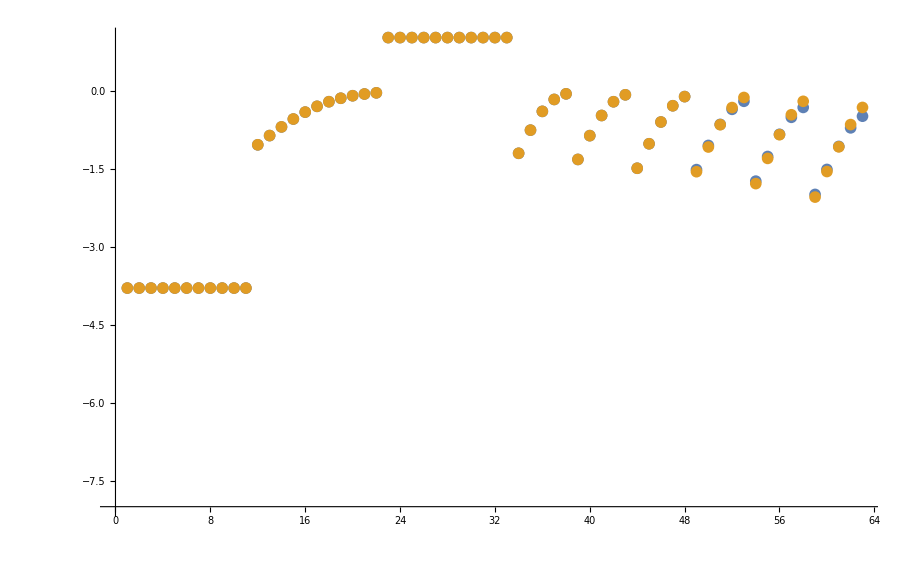

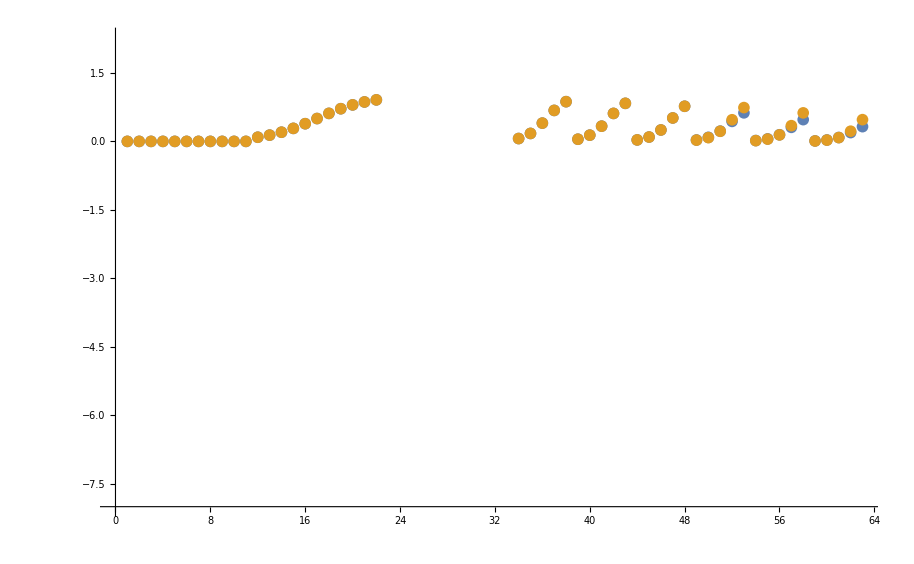

```mathematica
datasetI=100;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```



```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.00017 | 0.00017 | 1.54618×10^-6

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
10.5 | 10.5 | 8.98989×10^-10

```mathematica
haldaneRatiosList
```

{(k_FBA21^⟶ k_FBA22^⟶ k_FBA23^⟶ k_FBA24^⟶)/(k_FBA21^⟵ k_FBA22^⟵ k_FBA23^⟵ k_FBA24^⟵)}

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.00016 | 0.00016 | 3.66684×10^-9

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.00016 | 0.00016 | 2.15198×10^-6

```mathematica
backCalculateKic[fittingData[[-30;;-16,3]], filteredDataList[[1,3]][[-30;;-16]], fittingData[[-30;;-16,2]]//DeleteDuplicates, inhibitionList[[1,4]]]//TableForm
backCalculateKic[fittingData[[-15;;-1,3]], filteredDataList[[1,3]][[-15;;-1]], fittingData[[-15;;-1,4]]//DeleteDuplicates, inhibitionList[[2,4]]]//TableForm
backCalculateKiu[fittingData[[-15;;-1,3]], filteredDataList[[1,3]][[-15;;-1]], fittingData[[-15;;-1,4]]//DeleteDuplicates, inhibitionList[[3,4]]]//TableForm
```

data value | predicted value | error in %
0.00013 | 0.000130049 | 0.0374495

data value | predicted value | error in %
0.00003 | 0.0000300645 | 0.214852

data value | predicted value | error in %
0.00023 | 0.000228491 | 0.656204

```mathematica
inhibitionList
```

{{1,Kic,dhap,0.00013,{0.000119,0.000141},{},{{Competitive,fdp,0.00017}},M,8,30,{{trishcl,0.05}},{}},{1,Kincc,g3p,0.00003,{0.000025,0.000035},{},{{NonCompetitive,fdp,0.00017}},M,8,30,{{trishcl,0.05}},{}},{1,Kincu,g3p,0.00023,{0.000188,0.000272},{},{{NonCompetitive,fdp,0.00017}},M,8,30,{{trishcl,0.05}},{}}}

```mathematica
fittingData[[-15;;-1,3]]
```

{0.000017,0.0000537587,0.00017,0.000537587,0.0017,0.000017,0.0000537587,0.00017,0.000537587,0.0017,0.000017,0.0000537587,0.00017,0.000537587,0.0017}

```mathematica
fittingData[[-30;;-1]]
```

```mathematica
inhibitionList[[1,4]]
```

0.00013

#### Export rate back calculated parameter error distribution

```mathematica
fitLabel
```

p500_1

```mathematica
filteredDataList[[1,3]][[-15;;-1]]
```

{0.0303499,0.0885154,0.224697,0.437728,0.625995,0.0182298,0.0542825,0.144916,0.307152,0.476464,0.0101262,0.0305877,0.0847338,0.192584,0.323213}

```mathematica
inhibitionList
```

{{1,Kincc,g3p,0.00003,{0.000025,0.000035},{},{{NonCompetitive,fdp,0.00017}},M,8,30,{{trishcl,0.05}},{}},{1,Kincu,g3p,0.00023,{0.000188,0.000272},{},{{NonCompetitive,fdp,0.00017}},M,8,30,{{trishcl,0.05}},{}}}

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;

nRateSets=200;


rateConstList=Import[outputPath<>"/treated_data/rateconst_FBA2_" <>fitLabel<>"_"<>flagFitType<>".csv", "TSV"];

predictedParamsErrorList=Table[

(*paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];*)
paramFitSub=Thread[rateConstsSub[[All,1]]->rateConstList[[rateSetI,2;;]]];

{filteredDataList[[rateSetI,1]],
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName][[2;;,3]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2,3]],
backCalculateKic[fittingData[[-30;;-16,3]], filteredDataList[[rateSetI,3]][[-30;;-16]], fittingData[[-30;;-16,2]]//DeleteDuplicates, inhibitionList[[1,4]]][[2,3]],
backCalculateKic[fittingData[[-15;;-1,3]], filteredDataList[[rateSetI,3]][[-15;;-1]], fittingData[[-15;;-1,4]]//DeleteDuplicates, inhibitionList[[2,4]]][[2,3]],
backCalculateKiu[fittingData[[-15;;-1,3]], filteredDataList[[rateSetI,3]][[-15;;-1]], fittingData[[-15;;-1,4]]//DeleteDuplicates, inhibitionList[[3,4]]][[2,3]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub][[2,3]]}//Flatten,

{rateSetI, 1, nRateSets}];

predictedParamsErrorList=Insert[predictedParamsErrorList,{"ssd","Km_fdp", "kcat_f", "Kic_dhap", "Kincc_g3p", "Kincu_g3p", "Keq"},  1];
predictedParamsErrorList=Insert[predictedParamsErrorList,{0,kmList[[1]][[3]], kcatList[[1]][[3]], inhibitionList[[1,4]],inhibitionList[[2,4]],inhibitionList[[3,4]],  KeqList[[1,3]]}  ,2];
Export[outputPath<>"/treated_data/predicted_params_error_distribution"<>"_"<>fitLabel<>"_"<>flagFitType<>".csv",predictedParamsErrorList,"CSV"];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

```mathematica
enzymeModel["Reactions"]
```

{((FBA2^c)_^+fdp^c⇌(FBA2^c&fdp^c)_^)^FBA21,((FBA2^c&dhap^c)_^⇌(FBA2^c)_^+dhap^c)^FBA22,((FBA2^c&fdp^c)_^⇌(FBA2^c&dhap^c&g3p^c)_^)^FBA23,((FBA2^c&dhap^c&g3p^c)_^⇌(FBA2^c&dhap^c)_^+g3p^c)^FBA24,((FBA2^c)_^+dhap^c⇌(FBA2^c&dhap^c)_^)^FBA2_Kic_dhap_1_fdp,((FBA2^c)_^+g3p^c⇌(FBA2^c&g3p^c)_^)^FBA2_Kincc_g3p_1_fdp,((FBA2^c&g3p^c)_^+fdp^c⇌(FBA2^c&fdp^c&g3p^c)_^)^FBA2_NC_g3p,((FBA2^c&fdp^c)_^+g3p^c⇌(FBA2^c&fdp^c&g3p^c)_^)^FBA2_Kincu_g3p_1_fdp}